Amplitude Amplification |

Quantum Amplitude Amplification (AA)paclet:QuantumMob/Q3/tutorial/AmplitudeAmplification#1404287834 | Oblivious Amplitude Amplification (OAA)paclet:QuantumMob/Q3/tutorial/AmplitudeAmplification#635509592

Amplitude amplification is a quantum algorithmic technique used to increase the probability of finding a desired outcome in a quantum system. It generalizes the concept of Grover's algorithm, which is specifically designed for unstructured search problems. In amplitude amplification, the basic idea is to start with a superposition of quantum states, each with a certain amplitude, and iteratively apply a sequence of quantum operations to amplify the amplitudes of the states corresponding to desired outcomes while reducing the amplitudes of the undesired ones. This is achieved through a process involving quantum reflection and interference, which systematically increases the likelihood of measuring the correct state upon observation. The technique is widely applicable in quantum algorithms, providing a quadratic speedup over classical counterparts for a variety of search and optimization problems.

Quantum Amplitude Amplification (AA)

Consider a unitary operator U such that

ψ:=U0^(⊗n)=G √p+B √(1-p),

where G is the “good” (or desired) state and B is the “bad” state, GB=0, and p is the probability. It is assumed that although we do not have a direct access to the good state itself, we do have an access to the oracle

R_G:=I-2GG,

which “marks” the good state by the phase factor -1 or, equivalently, may be regarded as a reflection about the hyperplane perpendicular to G.

Following the idea behind the quantum search algorithm, we combine the oracle R_G and the reflection about the state ψ, 		
	R_ψ:=2ψψ-I_n=U(20^(⊗n)0^(⊗n)-I_n)U^†=U R_0 U^†, 
to get the rotation by angle 2θ (sinθ:=√p)

Ω_AA:=U R_0 U^†R_G

toward the desired state.

Technically, it is interesting to note that the amplitude amplification process Ω_AA preserves the two-dimensional subspace spanned by G and B as first observed by Brassard and Høyer (1997) and rediscovered by Grover (1998); see Figure 1.

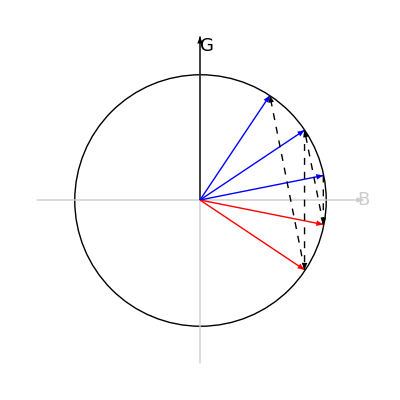

Figure 1. Geometric demonstration of the quantum amplitude amplification process.

Oblivious Amplitude Amplification (OAA)

Oblivious amplitude amplification (OAA) is a generalization of the quantum amplitude amplification algorithm. Unlike the standard amplitude amplification, OAA does not require knowledge of the initial state or a full reflection about it. Instead, it amplifies the amplitude of a target state while handling scenarios where the initial state is unknown or “oblivious.”

Let U be a unitary operator on the quantum register of n qubits. Consider an ancillary quantum register of m qubits, and let V be a unitary gate on the overall quantum register such that

V(0^(⊗m)⊗ψ)=0^(⊗m)⊗(Uψ)√p+Φ^⊥√(1-p),

where ΠΦ^⊥=0 with Π:=(0^(⊗m)0^(⊗m))⊗I_n. In the matrix form, the (m+n)⊗(m+n) unitary matrix V is a block encoding of n×n unitary matrix U,

V=(√p U | *
* | *) .

Here, it is important that U is unitary. The goal is to increase the success probability for 0^(⊗m) on the ancillary register.

If you follow the standard amplitude amplification idea in the above, you need an oracle

R_G:=(I_m⊗U)(I_(m+n)-20^(⊗m)0^(⊗m)⊗ψψ)(I_m⊗U^†)

and the reflection in V(0^(⊗m)⊗ψ),
	R_Ψ:=V(20^(⊗m)0^(⊗m)⊗ψψ-I_(m+n))V^†.

Note that both require an access to the initial state ψ or the reflection about it.

However, the OAA lemma (Berry et al., 2014https://doi.org/10.1145/2591796.2591854) asserts that the goal can be achieved by just repeatedly applying

Ω_OAA:=-UR U^†R    with    R:=(1-20^(⊗m)0^(⊗m))⊗I_n.

Here, the crucial point is that it does not require a copy (or knowledge) of the initial state ψ at all.

Another important point is that over the OAA process, the state remains in the two-dimensional subspace spanned by Φ:=0^(⊗m)⊗(Uψ) and Φ^⊥ (Berry et al., 2014https://doi.org/10.1145/2591796.2591854) as shown in Figure 2. This can be clearly seen by rewriting the unitary gate V as

VΨ=Φ √p+Φ^⊥√(1-p),

where Ψ:=0^(⊗m)⊗ψ, and defining a new state Ψ^⊥ through

VΨ^⊥=Φ √(1-p)-Φ^⊥√p.

One can see that not only ΨΨ^⊥=0 but also ΠΨ^⊥=0.

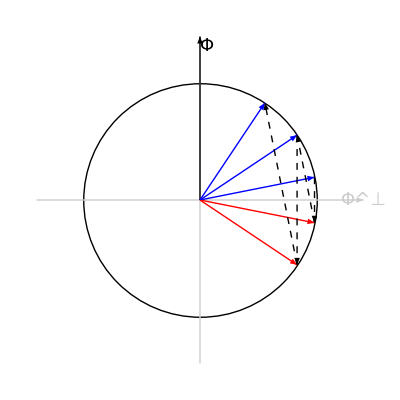

Figure 2. Geometric demonstration of the oblivious amplitude amplification process.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Search Algorithm
▪Quantum Computation: Overview
▪Quantum Information Systems with Q3

| Related Links
▪G . Brassard and P. Høyer (1997)https://doi.org/10.1109%2FISTCS.1997.595153, Proceedings of the Fifth Israeli Symposium on Theory of Computing and Systems, “An exact quantum polynomial-time algorithm for Simon’s problem.” 
▪Lov K . Grover (1998)https://doi.org/10.1103/PhysRevLett.80.4329, Physical Review Letters 80, 4329 (1998), “Quantum Computers Can Search Rapidly by Using Almost Any Transformation.”
▪D. W. Berry et al. (2014)https://doi.org/10.1145/2591796.2591854, Proceedings of the 2014 ACM symposium on Theory of Computing (STOC 2014), “Exponential improvement in precision ∗ for simulating sparse Hamiltonians.”
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).